## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="FBA2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy_r.csv";

mainFolder = "fit_FBA2_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological,Q10];
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; _fdp,g3p,dhap

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.000102656 | 0.0000975232
0.000107789 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00019 | 0.00016
0.00022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00024 | 0.00021
0.00027 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00085 | 0.0008075
0.0008925 |  | M | 7.5 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 19.941 | 18.6686
21.2704 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null | 15.516 | 14.6804
16.3326 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null | 19.6182 | 19.0484
20.1879 | 1/s | 8 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kic | dhap | 9.×10^-6 | 7.8×10^-6
0.0000102 |  | Competitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.000118 | 0.000095
0.000141 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.000221 | 0.000194
0.000248 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {10};
kmPriorities = {1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1,1};
inhibitionPriorities={0,0,0,0,0,0};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; _fdp,g3p,dhap

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
10 | fdp | Null | 0.000102656 | 0.0000975232
0.000107789 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00019 | 0.00016
0.00022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00024 | 0.00021
0.00027 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00085 | 0.0008075
0.0008925 |  | M | 7.5 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 19.941 | 18.6686
21.2704 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null | 15.516 | 14.6804
16.3326 | 1/s | 8 | 37 | trishcl | 0.05 | 
1 | fdp | Null | 19.6182 | 19.0484
20.1879 | 1/s | 8 | 37 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_FBA2[c] + fdp[c] <=> E_FBA2[c]&fdp",
				"E_FBA2[c]&fdp <=> E_FBA2[c]&dhap&g3p",
				"E_FBA2[c]&dhap&g3p <=> E_FBA2[c]&dhap + g3p[c]",
				"E_FBA2[c]&dhap <=> E_FBA2[c] + dhap[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,((FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c)^FBA22,((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,((FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c)^FBA24}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,Overscript[(FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c, FBA22],((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,Overscript[(FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c, FBA24]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={{"prod_inhib_dhap",m["g3p","c"]->0},{"prod_inhib_g3p",m["dhap","c"]->0}};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((FBA2^c&fdp^c)_^-((FBA2^c&dhap^c&g3p^c)_^)/K_FBA23) Volume_c k_FBA23^⟶}

Volume_c (-(FBA2^c&dhap^c&g3p^c)_^ k_FBA23^⟵+(FBA2^c&fdp^c)_^ k_FBA23^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating other relative rate forward equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
Variables[haldaneRatiosList[[1]]][[1]]
keqValCur = 0.000102656;
haldaneSub = Solve[keqValCur== haldaneRatiosList[[1]],Variables[haldaneRatiosList[[1]]][[1]]];
haldaneSub[[1,1]]
```

k_FBA21^⟵

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

k_FBA21^⟵→(9741.27 k_FBA21^⟶ k_FBA22^⟶ k_FBA23^⟶ k_FBA24^⟶)/(k_FBA22^⟵ k_FBA23^⟵ k_FBA24^⟵)

```mathematica
flux = 0.0006081074005408912;
FluxExpression = absoluteFlux /. {metabolite["fdp", "c"] -> 0.0010306264592820896,metabolite["g3p","c"]-> 0.00000539,
metabolite["dhap","c"]-> 0.000478,
     parameter["FBA2_total"] -> 0.0000051232949026178, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "FBA2"] /. FluxExpression/.haldaneSub[[1,1]];
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{3,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA2_total	param_pH	param_Temp	FileFlag	Target_Data
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
10	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt"	0.000102656
1	0	0.000017000000000000007	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.09090909090909094
1	0	0.00002694318427183895	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.1368068886032101
1	0	0.000042702069335662915	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.20076000891310194
1	0	0.0000676782189940945	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.28474724895080133
1	0	0.00010726274856163285	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.386863179846857
1	0	0.00017000000000000007	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.0002694318427183895	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0004270206933566291	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7152527510491988
1	0	0.0006767821899409458	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7992399910868985
1	0	0.0010726274856163284	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.0017000000000000008	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.9090909090909091
1	0	0.000018999999999999994	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.09090909090909087
1	0	0.00003011297065676116	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.13680688860321003
1	0	0.00004772584219868205	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.20076000891310186
1	0	0.0000756403624051644	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.2847472489508012
1	0	0.00011988189545123664	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.38686317984685686
1	0	0.00018999999999999996	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.49999999999999994
1	0	0.0003011297065676116	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0004772584219868205	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7152527510491987
1	0	0.0007564036240516448	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7992399910868982
1	0	0.0011988189545123664	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.8631931113967899
1	0	0.0018999999999999996	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.9090909090909092
1	0	0.000024000000000000018	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.09090909090909097
1	0	0.00003803743661906677	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.13680688860321016
1	0	0.00006028527435623002	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.20076000891310197
1	0	0.00009554572093283934	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.2847472489508014
1	0	0.00015142976267524643	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.38686317984685703
1	0	0.0002400000000000002	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.5000000000000002
1	0	0.0003803743661906677	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.6131368201531433
1	0	0.0006028527435623002	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7152527510491989
1	0	0.0009554572093283943	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7992399910868984
1	0	0.0015142976267524643	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.002400000000000002	0	1	8	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.9090909090909091
1	0	0.00008500000000000002	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.09090909090909093
1	0	0.00013471592135919474	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.1368068886032101
1	0	0.00021351034667831432	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.20076000891310175
1	0	0.00033839109497047284	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.2847472489508015
1	0	0.0005363137428081642	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.38686317984685703
1	0	0.0008500000000000003	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.5000000000000002
1	0	0.0013471592135919474	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.6131368201531433
1	0	0.0021351034667831453	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7152527510491987
1	0	0.0033839109497047284	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.7992399910868982
1	0	0.005363137428081642	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.8631931113967899
1	0	0.008500000000000002	0	1	7.5	30	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt"	0.9090909090909091
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.941017064474817
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	15.516010420643738
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
1	0	1	0	1	8	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt"	19.618162502478558
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912
3	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt"	0.0006081074005408912

### Simulate data with uncertainty

```mathematica
Null
```

```mathematica
Null
```

### Parameter scan

```mathematica
Null
```

```mathematica
Null
```

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateRev_dhap.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/otherRateRelFor_fdp_prod_inhib_dhap.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/otherRateRelFor_fdp_prod_inhib_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateFor_fdp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateRev_dhap.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/relRateRev_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/otherRateRelFor_fdp_prod_inhib_dhap.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/otherRateRelFor_fdp_prod_inhib_g3p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 20.7879287686
best_fit: 22.5497798046
best_fit: 20.772438274
best_fit: 20.771719065
best_fit: 21.2445661992
best_fit: 23.4301554231
best_fit: 30.6221375498
best_fit: 20.7836459318
best_fit: 22.6887863236
best_fit: 22.5967526032

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_FBA2_typeII/input/FBA2.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
10 | haldaneRatio_1 | 0.00220881 | 4.87883×10^-6 | 5.20779×10^-7 | 0.507305 | 0.000102656 | 0.000102135
1 | relRateFor_fdp | 0.0822846 | 0.00677075 | 0.0189641 | 20.8606 | 0.0909091 | 0.109873
1 | relRateFor_fdp | 0.0777381 | 0.00604322 | 0.0268168 | 19.6019 | 0.136807 | 0.163624
1 | relRateFor_fdp | 0.0714815 | 0.00510961 | 0.0359184 | 17.8912 | 0.20076 | 0.236678
1 | relRateFor_fdp | 0.0633995 | 0.0040195 | 0.0447555 | 15.7176 | 0.284747 | 0.329503
1 | relRateFor_fdp | 0.0537714 | 0.00289136 | 0.0509903 | 13.1804 | 0.386863 | 0.437853
1 | relRateFor_fdp | 0.0433476 | 0.00187902 | 0.0524813 | 10.4963 | 0.5 | 0.552481
1 | relRateFor_fdp | 0.0331682 | 0.00110013 | 0.0486614 | 7.93646 | 0.613137 | 0.661798
1 | relRateFor_fdp | 0.0241808 | 0.000584713 | 0.0409537 | 5.72576 | 0.715253 | 0.756206
1 | relRateFor_fdp | 0.0169259 | 0.000286486 | 0.031764 | 3.97428 | 0.79924 | 0.831004
1 | relRateFor_fdp | 0.0114817 | 0.000131829 | 0.0231251 | 2.67902 | 0.863193 | 0.886318
1 | relRateFor_fdp | 0.00761616 | 0.0000580058 | 0.0160832 | 1.76915 | 0.909091 | 0.925174
1 | relRateFor_fdp | 0.125012 | 0.015628 | 0.0303235 | 33.3559 | 0.0909091 | 0.121233
1 | relRateFor_fdp | 0.117763 | 0.0138682 | 0.0426133 | 31.1485 | 0.136807 | 0.17942
1 | relRateFor_fdp | 0.10786 | 0.0116339 | 0.0565979 | 28.1918 | 0.20076 | 0.257358
1 | relRateFor_fdp | 0.0951891 | 0.00906096 | 0.0697792 | 24.5057 | 0.284747 | 0.354526
1 | relRateFor_fdp | 0.0802647 | 0.00644242 | 0.0785322 | 20.2997 | 0.386863 | 0.465395
1 | relRateFor_fdp | 0.0643072 | 0.00413542 | 0.0797987 | 15.9597 | 0.5 | 0.579799
1 | relRateFor_fdp | 0.0489154 | 0.00239272 | 0.0730981 | 11.922 | 0.613137 | 0.686235
1 | relRateFor_fdp | 0.0354763 | 0.00125857 | 0.0608797 | 8.51163 | 0.715253 | 0.776132
1 | relRateFor_fdp | 0.0247265 | 0.000611398 | 0.0468249 | 5.85868 | 0.79924 | 0.846065
1 | relRateFor_fdp | 0.0167157 | 0.000279414 | 0.0338713 | 3.92396 | 0.863193 | 0.897064
1 | relRateFor_fdp | 0.0110563 | 0.000122241 | 0.0234407 | 2.57848 | 0.909091 | 0.932532
1 | relRateFor_fdp | 0.212833 | 0.0452977 | 0.057493 | 63.2423 | 0.0909091 | 0.148402
1 | relRateFor_fdp | 0.199187 | 0.0396756 | 0.0796121 | 58.1931 | 0.136807 | 0.216419
1 | relRateFor_fdp | 0.180862 | 0.0327111 | 0.103706 | 51.6569 | 0.20076 | 0.304466
1 | relRateFor_fdp | 0.157914 | 0.0249368 | 0.124865 | 43.8513 | 0.284747 | 0.409613
1 | relRateFor_fdp | 0.131553 | 0.0173062 | 0.136871 | 35.3796 | 0.386863 | 0.523734
1 | relRateFor_fdp | 0.104102 | 0.0108373 | 0.135437 | 27.0873 | 0.5 | 0.635437
1 | relRateFor_fdp | 0.0782838 | 0.00612835 | 0.121108 | 19.7523 | 0.613137 | 0.734245
1 | relRateFor_fdp | 0.0562291 | 0.00316171 | 0.0988676 | 13.8228 | 0.715253 | 0.81412
1 | relRateFor_fdp | 0.0388933 | 0.00151269 | 0.0748789 | 9.36877 | 0.79924 | 0.874119
1 | relRateFor_fdp | 0.0261418 | 0.000683395 | 0.0535545 | 6.20423 | 0.863193 | 0.916748
1 | relRateFor_fdp | 0.0172158 | 0.000296382 | 0.0367608 | 4.04369 | 0.909091 | 0.945852
1 | relRateFor_fdp | 0.623063 | 0.388208 | 0.290746 | 319.82 | 0.0909091 | 0.381655
1 | relRateFor_fdp | 0.558066 | 0.311438 | 0.357702 | 261.465 | 0.136807 | 0.494509
1 | relRateFor_fdp | 0.481178 | 0.231533 | 0.407173 | 202.816 | 0.20076 | 0.607933
1 | relRateFor_fdp | 0.397288 | 0.157838 | 0.426053 | 149.625 | 0.284747 | 0.7108
1 | relRateFor_fdp | 0.313224 | 0.098109 | 0.408895 | 105.695 | 0.386863 | 0.795758
1 | relRateFor_fdp | 0.235864 | 0.0556318 | 0.360664 | 72.1329 | 0.5 | 0.860664
1 | relRateFor_fdp | 0.170223 | 0.0289758 | 0.294225 | 47.9868 | 0.613137 | 0.907361
1 | relRateFor_fdp | 0.118449 | 0.0140301 | 0.224272 | 31.3556 | 0.715253 | 0.939525
1 | relRateFor_fdp | 0.0800546 | 0.00640874 | 0.161779 | 20.2416 | 0.79924 | 0.961019
1 | relRateFor_fdp | 0.0529384 | 0.00280248 | 0.111901 | 12.9636 | 0.863193 | 0.975094
1 | relRateFor_fdp | 0.034471 | 0.00118825 | 0.0750978 | 8.26075 | 0.909091 | 0.984189
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.619974 | 0.384367 | 63.1819 | 316.844 | 19.941 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.728941 | 0.531355 | 67.6069 | 435.724 | 15.516 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
1 | absRateFor | 0.627063 | 0.393207 | 63.5048 | 323.704 | 19.6182 | 83.1229
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339
3 | customRatio_1 | 0.220097 | 0.0484427 | 0.000241768 | 39.7575 | 0.000608107 | 0.000366339

### Simulated Data and Best Fit Data Plot

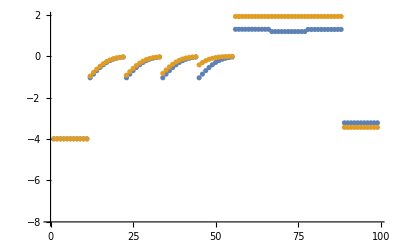

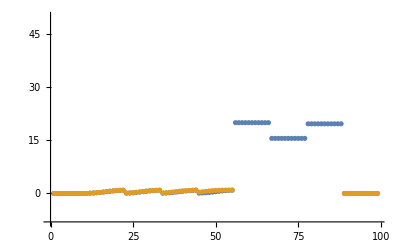

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

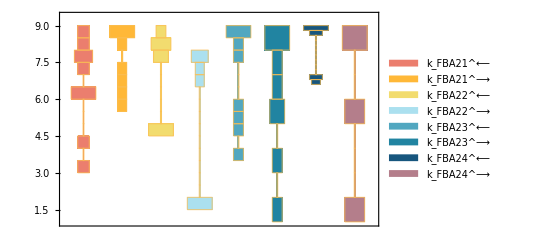

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

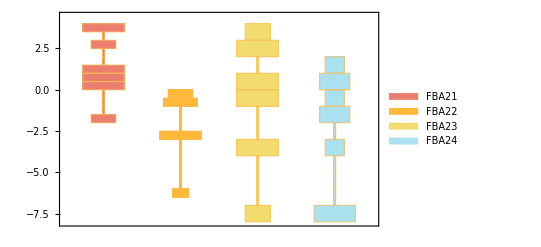

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

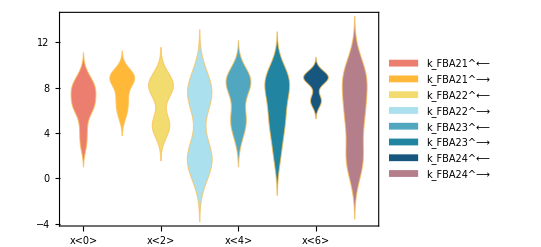

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

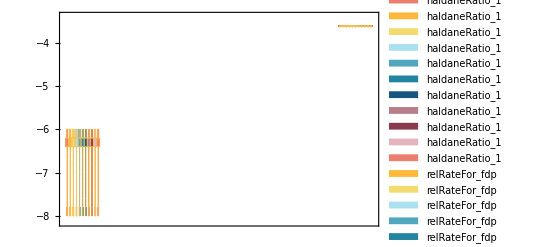

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.00017 | 0.000137707 | 18.9958
0.00019 | 0.000137707 | 27.5226
0.00024 | 0.000137707 | 42.622
0.00085 | 0.000137707 | 83.7992

```mathematica
assumedSaturatingConc
```

1

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
19.941 | 83.1229 | 316.844
15.516 | 83.1229 | 435.724
19.6182 | 83.1229 | 323.704

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.000102656 | 0.000102135 | 0.507305

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.000102656 | 0.000102135 | 0.507305

```mathematica
MASSef
```

MASSef

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

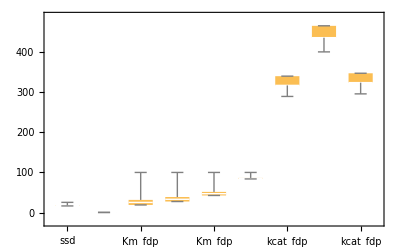

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 10;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/fba2 already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/fba2\rateconst_labels_fba2.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/fba2\S_fba2.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_FBA2[c],E_FBA2[c]&dhap,E_FBA2[c]&fdp,dhap[c],fdp[c],g3p[c],E_FBA2[c]&dhap&g3p}

/Users/guest/Desktop/internship stuff/MASSef/examples/fba2\species_fba2.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{FBA21: E_FBA2[c] + fdp[c] <=> E_FBA2[c]&fdp,FBA22: E_FBA2[c]&dhap <=> dhap[c] + E_FBA2[c],FBA23: E_FBA2[c]&fdp <=> E_FBA2[c]&dhap&g3p,FBA24: E_FBA2[c]&dhap&g3p <=> E_FBA2[c]&dhap + g3p[c]}

/Users/guest/Desktop/internship stuff/MASSef/examples/fba2\reactions_fba2.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_FBA2[c],E_FBA2[c]&dhap,E_FBA2[c]&fdp,E_FBA2[c]&dhap&g3p}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_FBA21_rev*k_FBA22_fwd*k_FBA23_rev*param_FBA2_total) - k_FBA21_rev*k_FBA22_fwd*k_FBA24_fwd*param_FBA2_total - k_FBA22_fwd*k_FBA23_fwd*k_FBA24_fwd*param_FBA2_total - g3p(c)*k_FBA21_rev*k_FBA23_rev*k_FBA24_rev*param_FBA2_total)/(fdp(c)*k_FBA21_fwd*k_FBA22_fwd*k_FBA23_fwd + fdp(c)*k_FBA21_fwd*k_FBA22_fwd*k_FBA23_rev + k_FBA21_rev*k_FBA22_fwd*k_FBA23_rev + dhap(c)*k_FBA21_rev*k_FBA22_rev*k_FBA23_rev + fdp(c)*k_FBA21_fwd*k_FBA22_fwd*k_FBA24_fwd + k_FBA21_rev*k_FBA22_fwd*k_FBA24_fwd + dhap(c)*k_FBA21_rev*k_FBA22_rev*k_FBA24_fwd + fdp(c)*k_FBA21_fwd*k_FBA23_fwd*k_FBA24_fwd + k_FBA22_fwd*k_FBA23_fwd*k_FBA24_fwd + dhap(c)*k_FBA22_rev*k_FBA23_fwd*k_FBA24_fwd + dhap(c)*g3p(c)*k_FBA21_rev*k_FBA22_rev*k_FBA24_rev + fdp(c)*g3p(c)*k_FBA21_fwd*k_FBA23_fwd*k_FBA24_rev + dhap(c)*g3p(c)*k_FBA22_rev*k_FBA23_fwd*k_FBA24_rev + fdp(c)*g3p(c)*k_FBA21_fwd*k_FBA23_rev*k_FBA24_rev + g3p(c)*k_FBA21_rev*k_FBA23_rev*k_FBA24_rev + dhap(c)*g3p(c)*k_FBA22_rev*k_FBA23_rev*k_FBA24_rev))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/fba2\rateconst_clusters_fba2.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/fba2\rateLaw_fba2.txt